```mathematica
Clear["Global`*"]
(*Defififinition of f=f(x,t)*)
f[x_,t_]= x^2;
(*Error message*)
approximate::nonnegativeint="'N' must be replaced by a non-negative integer.";

(*Construction of successively approximate sequences t:time;x0:initial value;N:number of iterations The initial time t0 is always 0*)

approximate[t_,x0_,N_]:=Module[{k=0}, If[Or[N<0,Not[IntegerQ[N]]],Message[approximate::nonnegativeint,N],
x[0,s_]:=x0;
While[k<N,
x[k_,s_]:=(x[k,s]=x0+Integrate[f[x[k−1,u],u],{u,0,s}]);
k++];(*Instead of “While,” you can also use “For” and “Do”*)
x[N,t]
]
];
(*An example of “approximate”*)
approximate[1,1,7]
```

2279484092449900682074021619525178168414129521633376281710921070161286743803362906465595032705904140748807903477397594451/110259043244440018713915981462002281136202324242020824939148362935682774135059389235300388292914942514494578688000000000

{{0.,1.},{0.1,1.11111},{0.2,1.24999},{0.3,1.42848},{0.4,1.6659},{0.5,1.99533},{0.6,2.47619},{0.7,3.2206},{0.8,4.45062},{0.9,6.62702},{1.,10.747}}

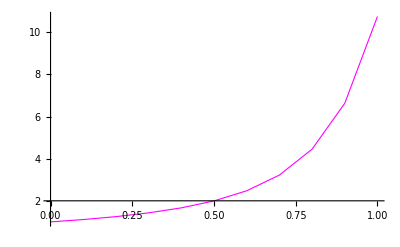

```mathematica
(*Numerical solution (data):k=number of iterations;d=[step size];tlast=[last time]*)nsol[k_,d_,x0_,tlast_]:=Table[{t,approximate[t,x0,k]},{t,0,tlast,d}];

ngraph[k_,d_,x0_,tlast_]:=ListLinePlot[nsol[k,d,x0,tlast],PlotStyle->{Thickness[0.002],RGBColor[1,0,1]},PlotRange->All];
(*Graph of the numerical solution:k=3;d=0:1;x0=1;tlast=10*)
nsol[5,0.1,1,1]
ngraph[5,0.1,1,1]
```

```mathematica
(*Analytical solution:x0=1*)
asol[x0_]:=DSolve[{x '[t]==f[x[t],t],x[0]==x0},x[t],t];
asol[1]
```

{{x[t]→1/(1-t)}}

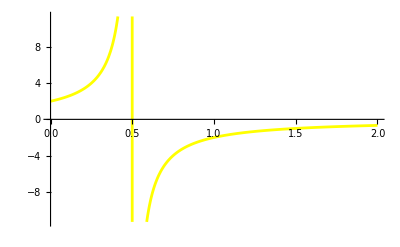

```mathematica
(*Graph of the analytical solution:x0=1;tlast=10*) agraph[x0_,tlast_]:=Plot[Evaluate[x[t]/.asol[x0]],{t,0,tlast},PlotStyle->{Thickness[0.005],RGBColor[1,1,0]}]
agraph[2,2]
```

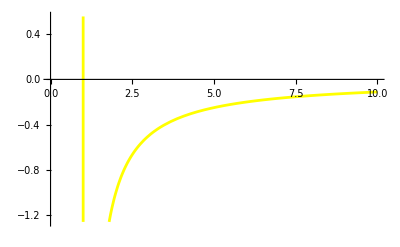

```mathematica
(*Graph of the analytical solution:x0=1;tlast=10*) agraph[x0_,tlast_]:=Plot[Evaluate[x[t]/.asol[x0]],{t,0,tlast},PlotStyle->{Thickness[0.005],RGBColor[1,1,0]}]
agraph[1,10]
```

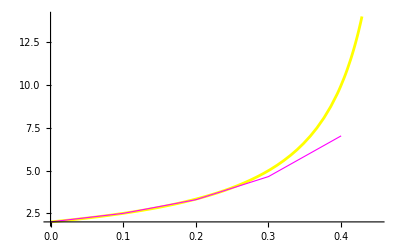

```mathematica
Show[agraph[2,0.45],ngraph[10,0.1,2,0.45]]
```

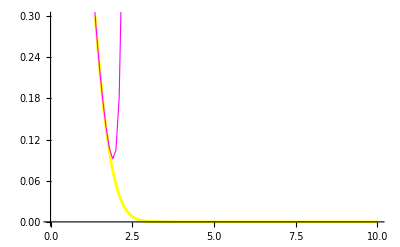

```mathematica
Show[agraph[1,10],ngraph[10,0.1,1,10]]
```